## Read This First

The combinatorics of fully packed loops and Razumov-Stroganov conjectures
A Mathematica-based presentation

Copyright (c) 2014 Dan Romik. You may distribute this document freely for all noncommercial purposes as long as it is kept in its original unmodified form. You may freely modify, use and distribute the Mathematica source code contained in the initialization code blocks below, but not other parts of the document. If you distribute any derivative works based on the code, an acknowledgement to the author is appreciated.

### Initialization code (for geeks)

#### Function Library, part 1

The Mathematica package linkpatterns.m I wrote in 2012-2014. It implements many functions and algorithms related to noncrossing matchings, the Temperley-Lieb random walk, wheel polynomials and other concepts described in my paper “Connectivity patterns in loop percolation I: the rationality phenomenon and constant term identities”

```mathematica
(*
linkpatterns, a Mathematica 8 software package by Dan Romik
Version 1.1
Copyright (c) Dan Romik 2014

Package documentation
---------------------

1. General information
----------------------

LinkPatternsInfoMessage[]
	Prints an info message (called automatically when package is loaded)
	
LinkPatternsHelp[]
	Displays detailed help information

2. Manipulation of link patterns and related objects
----------------------------------------------------

NumLinkPatterns[n]
	Returns the number of link patterns of order n (the nth Catalan number: 1,2,5,14,42,132,429,...)

LinkPatterns[n]
	Returns a list of all link patterns of order n. Each link pattern is represented as a sequence of +1 and -1's
	encoding a Dyck path, with +1's encoding an up step and -1's encoding down steps
	
MinimalLinkPattern[n]
	Returns the minimal link pattern of order n (n nested arches)
	
MaximalLinkPattern[n]
	Returns the maximal link pattern of order n	(n little arches side by side)

NoncrossingMatchings[n]
	Returns a list of noncrossing matchings of order n (each matching represented as a permutation)
	
LinkPatternToNoncrossingMatching[linkpattern]
	Returns the noncrossing matching associated with a given link pattern
		
NoncrossingMatchingToLinkPattern[noncrossingmatching]
	Returns the link pattern associated with a given noncrossing matching
	
LinkPatternToYoungDiagram[linkpattern]
	Returns the Young diagram (a subset of the staircase diagram) associated with a given link pattern
	
LinkPatternToDyckPath[linkpattern]
	Returns the Dyck path associated with a given link pattern

Arches[linkpattern]
	Returns a list of pairs of elements representing the arches in a link Pattern
	
LittleArches[linkpattern, wraparound]
	Returns a list of the "little arches" (matched adjacent elements) in a link Pattern,
	including the maximal arch (1,2n) if the boolean value "wraparound" is true 
	
LittleArches[linkpattern]
	Same as calling LittleArches[linkpattern, True]
	
NumberOfLittleArches[linkpattern, wraparound]
	Returns the length of LinkPattern[linkpattern, wraparound]
	
NumberOfLittleArches[linkpattern]
	Returns the length of LinkPattern[linkpattern]
	
LittleArch[linkpattern]
	Returns an arbitrary little arch of the link Pattern
	
OpeningPositions[linkpattern]
	Returns the positions of the +1's in a link pattern
	
RotateLinkPatternForward[linkpattern]
	Returns the link pattern rotated counterclockwise (i.e. element 1 is relabeled 2, 2 is relabeled 3 etc.)
	
RotateLinkPatternBack[linkpattern]
	Returns the link pattern rotated clockwise (i.e. element 2 is relabeled 1, 3 is relabeled 2 etc.)
	
	
	
3. Graphical representations of link patterns
---------------------------------------------

LinkPatternGraphicsCircular[linkpattern, numbered]
	Returns a graphical representation of a link pattern arranged in a circle. If the boolean value "numbered" is true
	then textual numbering is added.

LinkPatternGraphicsLinear[linkpattern, numbered]
	Returns a graphical representation of a link pattern arranged on a line. If the boolean value "numbered" is true 
	then textual numbering is added.
	
LinkPatternGraphicsDyckPath[linkpattern, numbered, showlinks, showyoungdiagram]
	Returns a graphical representation of a link pattern as a Dyck path.
	If the boolean value "numbered" is true then textual numbering is added.
	If the boolean value "showlinks" is true then lines indicating the matching links are added.
	If the boolean value "showyoungdiagram" is true then the associated Young diagram is shown.
	
LinkPatternGraphicsYoungDiagram[linkpattern]
	Returns a graphical representation of the Young diagram associated with the link pattern.
	
NoncrossingMatchingGraphicsCircular[matching, numbered]
	Similar to LinkPatternGraphicsCircular[linkpattern, numbered] but the input is encoded as a noncrossing matching

NoncrossingMatchingGraphicsLinear[matching, numbered]
	Similar to LinkPatternGraphicsLinear[linkpattern, numbered] but the input is encoded as a noncrossing matching


4. The Razumov-Stroganov distribution
-------------------------------------
	
RazumovStroganovEigenvector[n]
	Returns the ground state eigenvector of the Hamiltonian associated with the Razumov-Stroganov
	random walk on link patterns, normalized to have minimal coordinate 1

RandomLinkPattern[n]
	Samples a (pseudo)random link pattern from the Razumov-Stroganov distribution of order n
	

5. Wheel polynomials
--------------------

LPPolynomialsOfSecondKind[seq, var]
	Computes the link pattern polynomial of the second kind ("\Phi_a(z)") associated with the sequence seq
	and the variable symbol var
	
LPPolynomialsOfSecondKindEvaluateAtOne[seq]
	Computes the value at z=(1,1,...,1) of the link pattern polynomial of the second kind associated
	with the sequence seq

LPPolynomialsConversionCoefficient[seq, linkpattern]
	Computes the coefficient of Psi_linkpattern in the linear expansion of Phi_seq in the link pattern basis
	
LPPolynomialsConversionCoefficientVariant[linkpattern1, linkpattern2]
	Same as LPPolynomialsConversionCoefficient[seq, linkpattern2] where seq is the opening positions sequence
	of linkpattern1
	
LPPolynomialChangeOfBasisMatrix[order]
	Computes the change of basis matrix between the link pattern polynomial bases of the first and second kinds
	of given order
	
LPPolynomialInverseChangeOfBasisMatrix[order]
	Computes the change of basis matrix between the link pattern polynomial bases of the second and first kinds
	of given order (the inverse matrix of LPPolynomialChangeOfBasisMatrix[order])


*)

LinkPatternsInfoMessage[]:=Module[{},
	Print["linkpatterns version 1.1\nCopyright (c) 2014 Dan Romik\nType LinkPatternsHelp[] for more information"];
];

LinkPatternsHelp[]:=Print["Package Documentation is included as a comment block in the source file"] (* TODO add this *)

LinkPatternsInfoMessage[];

NumLinkPatterns[n_]:=CatalanNumber[n];

ListProduct[a_,b_]:=Flatten[Table[Join[a[[i]],b[[j]]],{i,1,Length[a]},{j,1,Length[b]}],1];

LinkPatterns[n_]:=If[n==0,{{}},
	Apply[Join,Table[ListProduct[ListProduct[ListProduct[{{1}},LinkPatterns[k-1]],{{-1}}],LinkPatterns[n-k]],{k,1,n}]]
];

MinimalLinkPattern[order_]:=Join[Table[1,{i,1,n}],Table[-1,{i,1,n}]];

MaximalLinkPattern[order_]:=Flatten[Table[{1,-1},{i,1,n}]];

MatchingPartner[linkpattern_,element_]:=Module[{i,s},
	If[linkpattern[[element]]==1,
		(s=1;i=element;While[s>0,i=i+1;s=s+linkpattern[[i]]];i),
		(s=1;i=element;While[s>0,i=i-1;s=s-linkpattern[[i]]];i)
	]
];

LinkPatternToNoncrossingMatching[linkpattern_]:=Table[MatchingPartner[linkpattern,i],{i,1,Length[linkpattern]}];

LinkPatternToDyckPath[linkpattern_]:=Module[{d, len},
	len=Length[linkpattern]/2;
	d=Table[0,{j,1,2len+1}];
	Do[d[[j]]=d[[j-1]]+linkpattern[[j-1]],{j,2,2len}];
	d
];

LinkPatternToYoungDiagram[linkpattern_]:=Module[{len,positions},
	len=Length[linkpattern]/2;
	positions=Map[First,Position[linkpattern,1]];
	Reverse[Table[positions[[j]]-j,{j,2,len}]]
];

NoncrossingMatchingToLinkPattern[noncrossingmatching_]:=Table[If[noncrossingmatching[[j]]>j,1,-1],
																{j,1,Length[noncrossingmatching]}];

NoncrossingMatchings[n_]:=Map[LinkPatternToNoncrossingMatching,LinkPatterns[n]];

ApplyTLOperatorToLinkPattern[linkpattern_,index_]:=Module[{newlinkpattern,partner,index2,partner2},
	newlinkpattern=linkpattern;
	index2=index+1;
	If[index2>Length[linkpattern],index2=1];
	partner=MatchingPartner[linkpattern,index];
	partner2=MatchingPartner[linkpattern,index2];
	If[partner!=index2,
		newlinkpattern[[partner]]=If[partner<partner2,1,-1];
		newlinkpattern[[partner2]]=If[partner<partner2,-1,1];
		If[index2==1,
			newlinkpattern[[index]]=-1;newlinkpattern[[index2]]=1,
			newlinkpattern[[index]]=1;newlinkpattern[[index2]]=-1;]];
	newlinkpattern
];

TLOperatorMatrix[order_,index_]:=Module[{linkpatterns,size,matrix,linkpattern2,j},
	linkpatterns=LinkPatterns[order];
	size=Length[linkpatterns];
	matrix=Table[0,{i,1,size},{j,1,size}];
	Do[linkpattern2=ApplyTLOperatorToLinkPattern[linkpatterns[[i]],index];
	j=Position[linkpatterns,linkpattern2][[1]][[1]];
	matrix[[j]][[i]]=1,{i,1,size}];
	matrix
];
	
RazumovStroganovMatrix[order_]:=Sum[TLOperatorMatrix[order,index],{index,1,2 order}];

RazumovStroganovEigenvector[order_]:=First[
	NullSpace[RazumovStroganovMatrix[order]-2 order IdentityMatrix[CatalanNumber[order]]]
];

RazumovStroganovAperiodicMatrix[order_]:=Sum[TLOperatorMatrix[order,index],{index,1,2 order-1}];

RazumovStroganovAperiodicEigenvector[order_]:=First[
	NullSpace[RazumovStroganovAperiodicMatrix[order]-(2 order-1) IdentityMatrix[CatalanNumber[order]]]
];


LinkPatternRightNestingLevels[linkpattern_]:=Module[{len,dyck,noncrossingmatching},
	len=Length[linkpattern]/2;
	dyck=Table[0,{j,1,2len+1}];
	noncrossingmatching=LinkPatternToNoncrossingMatching[linkpattern];
	Do[dyck[[j]]=dyck[[j-1]]+linkpattern[[j-1]],{j,2,2 len}];
	Table[Max[Table[dyck[[i]]-dyck[[Min[j,noncrossingmatching[[j]]]]],
			{i,Min[j,noncrossingmatching[[j]]],Max[j,noncrossingmatching[[j]]]}]],{j,1,2 len}]
];

LinkPatternLeftNestingLevels[linkpattern_]:=Module[{len,dyck,noncrossingmatching},
	len=Length[linkpattern]/2;
	dyck=Table[0,{j,1,2len+1}];
	noncrossingmatching=LinkPatternToNoncrossingMatching[linkpattern];
	Do[dyck[[j]]=dyck[[j-1]]+linkpattern[[j-1]],{j,2,2 len}];
	Table[Max[Max[Table[dyck[[i]]-dyck[[Min[j,noncrossingmatching[[j]]]]],
						{i,Max[j,noncrossingmatching[[j]]],2 len+1}]],
					Max[Table[dyck[[i]]-dyck[[Min[j,noncrossingmatching[[j]]]]],
						{i,1,Min[j,noncrossingmatching[[j]]]}]]],{j,1,2 len}]
];

Arches[linkpattern_]:=Module[{noncrossingmatching},
	noncrossingmatching=LinkPatternToNoncrossingMatching[linkpattern];
	Union[Table[{Min[j,noncrossingmatching[[j]]],Max[j,noncrossingmatching[[j]]]},
					{j,1,Length[noncrossingmatching]}]]
];

LittleArch[linkpattern_]:=Module[{pos},pos=1;While[linkpattern[[pos]]!=1||linkpattern[[pos+1]]!=-1,pos=pos+1];pos];

OpeningPositions[linkpattern_]:=Map[First,Position[linkpattern,1]];

LittleArches[linkpattern_,wraparound_]:=Module[{arches,len},
	arches=Arches[linkpattern];
	len=Length[linkpattern];
	Select[arches,#[[2]]==#[[1]]+1 || (wraparound && #[[2]]==#[[1]]+len-1)&]
];

LittleArches[linkpattern_]:=LittleArches[linkpattern,True];

NumberOfLittleArches[linkpattern_, wraparound_]:=Length[LittleArches[linkpattern, wraparound]];

NumberOfLittleArches[linkpattern_]:=Length[LittleArches[linkpattern]];

RotateLinkPatternForward[linkpattern_]:=Module[{PartnerOfLastElement},
	PartnerOfLastElement=Last[LinkPatternToNoncrossingMatching[linkpattern]];
	Join[{1},
		 linkpattern[[Range[1,PartnerOfLastElement-1]]],
		 {-1},
		 linkpattern[[Range[PartnerOfLastElement+1,Length[linkpattern]-1]]]]
]

RotateLinkPatternBack[linkpattern_]:=Module[{PartnerOfFirstElement},
	PartnerOfFirstElement=First[LinkPatternToNoncrossingMatching[linkpattern]];
	Join[linkpattern[[Range[2,PartnerOfFirstElement-1]]],
		 {1},
		 linkpattern[[Range[PartnerOfFirstElement+1,Length[linkpattern]]]],
		 {-1}]
]





LinkPatternGraphicsCircular[linkpattern_,numbered_]:=Module[{len,noncrossingmatching,nestinglevels,nestinglevels1,nestinglevels2},
	len=Length[linkpattern]/2;
	noncrossingmatching=LinkPatternToNoncrossingMatching[linkpattern];
	nestinglevels1=LinkPatternRightNestingLevels[linkpattern];
	nestinglevels2=LinkPatternLeftNestingLevels[linkpattern];
	nestinglevels=Table[Min[nestinglevels1[[j]],nestinglevels2[[j]]],{j,1,Length[nestinglevels1]}];
	Graphics[Join[{Circle[]},
					Table[Disk[{Cos[Pi+(n-1) Pi/len],Sin[Pi+(n-1) Pi/len]},0.4/(len+10)],{n,1,2 len}],
					Union[Table[BezierCurve[
									{{Cos[Pi+(Min[n,noncrossingmatching[[n]]]-1) Pi/len],
										Sin[Pi+(Min[n,noncrossingmatching[[n]]]-1) Pi/len]},
									 {(1-2nestinglevels[[n]]/(len+1))(Cos[Pi+(n-1)Pi/len]
									 	+Cos[Pi+(noncrossingmatching[[n]]-1)Pi/len])/2,
									  (1-2nestinglevels[[n]]/(len+1))(Sin[Pi+(n-1)Pi/len]
									 	+Sin[Pi+(noncrossingmatching[[n]]-1)Pi/len])/2},
									 {Cos[Pi+(Max[n,noncrossingmatching[[n]]]-1) Pi/len],
									  Sin[Pi+(Max[n,noncrossingmatching[[n]]]-1) Pi/len]}}
								],{n,1,2 len}]],
					If[numbered,
						Table[Text[Style[n,18],{1.1 Cos[Pi+(n-1) Pi/len],1.1 Sin[Pi+(n-1) Pi/len]}],{n,1,2 len}],
						{}]]
			]
];
	
LinkPatternGraphicsLinear[linkpattern_, numbered_] := Module[{len, noncrossingmatching, nestinglevels, dyck}, 
   len = Length[linkpattern]/2;
   noncrossingmatching = LinkPatternToNoncrossingMatching[linkpattern];
   dyck = Table[0, {j, 1, 2 len}];
   Do[dyck[[j]] = dyck[[j - 1]] + linkpattern[[j]], {j, 2, 2 len}];
   nestinglevels = LinkPatternRightNestingLevels[linkpattern];
   Graphics[
		Join[{AbsoluteThickness[1.5],Line[{{0.5, 0}, {2 len + 0.5, 0}}]}, 
			Table[Disk[{n, 0}, 2/(len + 10)], {n, 1, 2 len}], 
			Union[Table[
				{
					Circle[{Min[n, noncrossingmatching[[n]]] + nestinglevels[[n]] - 1/2, 0}, nestinglevels[[n]] - 1/2, {Pi/2, Pi}],
					Circle[{Max[n, noncrossingmatching[[n]]] - nestinglevels[[n]] + 1/2, 0}, nestinglevels[[n]] - 1/2, {0, Pi/2}],
					If[Min[n, noncrossingmatching[[n]]]+nestinglevels[[n]]-1/2<Max[n,noncrossingmatching[[n]]]-nestinglevels[[n]]+ 1/2, 
						Line[{{Min[n, noncrossingmatching[[n]]] + nestinglevels[[n]] - 1/2, nestinglevels[[n]] - 1/2}, 
							  {Max[n, noncrossingmatching[[n]]] - nestinglevels[[n]] + 1/2, nestinglevels[[n]] - 1/2}}], {}
					  ]
				}, {n, 1, 2 len}]], 
			If[numbered, Table[Text[Style[n, 14], {n, -0.6}], {n, 1, 2 len}], {}]]
   ]
];

NoncrossingMatchingGraphicsCircular[matching_, numbered_] :=
  LinkPatternGraphicsCircular[NoncrossingMatchingToLinkPattern[matching],numbered];

NoncrossingMatchingGraphicsLinear[matching_, numbered_] :=
  LinkPatternGraphicsLinear[NoncrossingMatchingToLinkPattern[matching],numbered];



LinkPatternGraphicsDyckPath[linkpattern_,numbered_,showlinks_,showyoungdiagram_]:=Module[
	{len,noncrossingmatching,dyckpath,nestinglevels,positions1,positions2},
	len=Length[linkpattern]/2;
	noncrossingmatching=LinkPatternToNoncrossingMatching[linkpattern];
	dyckpath=LinkPatternToDyckPath[linkpattern];
	nestinglevels=LinkPatternRightNestingLevels[linkpattern];
	positions1=Map[First,Position[linkpattern,-1]];
	positions2=Map[First,Position[linkpattern,1]];
	Graphics[Join[{Line[{{0,0},{2len+1,0}}],Line[Map[{#-1,dyckpath[[#]]}&,Range[2len+1]]]},
			 If[showyoungdiagram,
			 	{{GrayLevel[0.9],Polygon[Append[Map[{#-1,dyckpath[[#]]}&,Range[2len+1]],{len,len}]]},
			 	 Table[Line[{{2(j-1)+dyckpath[[positions1[[j]]]],dyckpath[[positions1[[j]]]]},{len+j-1,len-j+1}}],
			 	 		{j,1,len}],
				 Table[Line[{{positions2[[j]],dyckpath[[positions2[[j]]]]+1},{j,j}}],{j,1,len}]},
				{}
			   ],
			 If[numbered,{Table[Disk[{j-0.5,0},0.1],{j,1,2 len}],Table[Text[Style[j,20],{j-0.5,-0.5}],{j,1,2 len}]},{}],
			 If[showlinks,Union[Table[{Dashing[{0.01,0.01}],
									  Line[{{-0.5+Min[j,noncrossingmatching[[j]]],len+0.5},
											{-0.5+Min[j,noncrossingmatching[[j]]],dyckpath[[Min[j,noncrossingmatching[[j]]]]]+0.5},
											{-0.5+Max[j,noncrossingmatching[[j]]],dyckpath[[Min[j,noncrossingmatching[[j]]]]]+0.5},
											{-0.5+Max[j,noncrossingmatching[[j]]],len+0.5}}]},{j,1,2 len}]],{}]]
	]
];

LinkPatternGraphicsParticles[linkpattern_,numbered_]:=Module[{len,particles,holes},
	len=Length[linkpattern]/2;
	particles=Map[First,Position[linkpattern,1]];
	holes=Map[First,Position[linkpattern,-1]];
	Graphics[Join[{Line[{{0,0},{2 len,0}}],
				   Table[Disk[{particles[[j]]-0.5,0},0.2],{j,1,len}],
				   Table[Circle[{holes[[j]]-0.5,0},0.1],{j,1,len}]},
				   If[numbered,Table[Text[j,{j-1/2,-1/2}],{j,1,2 len}],{}]]
			]
];

RemoveTrailingZeros[diag_]:=Module[{p},p=Position[diag,0];If[Length[p]==0,diag,diag[[Range[p[[1]][[1]]-1]]]]];

LinkPatternGraphicsYoungDiagram[linkpattern_]:=Module[{diag,diag2},
	diag=RemoveTrailingZeros[LinkPatternToYoungDiagram[linkpattern]];
	diag2=RemoveTrailingZeros[Table[Length[Select[diag, # >= j &]], {j, 1, Max[Append[diag,0]]}]];
	If[diag=={},
	   Graphics[],
	   Graphics[Join[{Line[{{0,0},{diag[[1]],0}}],Line[{{0,0},{0,-diag2[[1]]}}]},
					  Table[Line[{{0,-j},{diag[[j]],-j}}],{j,1,Length[diag]}],
					  Table[Line[{{j,0},{j,-diag2[[j]]}}],{j,1,Length[diag2]}]]
			   ]
	  ]
];



(* Code for sampling random link patterns from the Razumov-Stroganov distribution *)

InitialDoubleSidedLinkPattern[n_]:=Table[1+Mod[i-1+2n,4n],{i,1,4n}];

ApplyTLOperatorToDSLP[lp_,index_]:=Module[{order,index2,partner,partner2,newlp},
	order=Length[lp]/4;
	index2=index+1;If[index2>2 order,index2=1];
	partner=lp[[index]];
	partner2=lp[[index2]];
	disconnectedflag=(partner>2 order&&partner2>2 order);
	newlp=lp;
	If[partner!=index2,
		newlp[[index]]=index2;newlp[[index2]]=index;newlp[[partner]]=partner2;newlp[[partner2]]=partner
	  ];
	newlp
];

DSLPDisconnectedQ[lp_]:=Module[{halflength},
	halflength=Length[lp]/2;
	Apply[And,Table[lp[[i]]<=halflength,{i,1,halflength}]]
];

RandomLinkPattern[order_]:=Module[{lp,count,twiceorder},
	twiceorder=2 order;
	lp=InitialDoubleSidedLinkPattern[order];
	doublesidedconnections=order;
	While[doublesidedconnections>0,
			lp=ApplyTLOperatorToDSLP[lp,Random[Integer,{1,twiceorder}]];
			If[disconnectedflag,doublesidedconnections=doublesidedconnections-1]
		 ];
	NoncrossingMatchingToLinkPattern[lp[[Range[twiceorder+1,4 order]]]-twiceorder]
]



MultiCartesianProduct[lists_]:=Flatten[Apply[Outer,Join[{List},lists]],Length[lists]-1]

(* Old routine for computing link pattern polynomials of the second kind - keeping for future reference *)
(*
NilpPolynomialOld[linkpattern_, var_]:=Module[{len,positions,vectors,prefactor,sum},len=Length[linkpattern]/2;positions=First/@Position[linkpattern,1];
vectors=MultiCartesianProduct[Table[Range[positions[[j]]],{j,1,len}]];
prefactor=(-1)^(len (len-1)/2)Product[q var[j]-q^(-1) var[k],{j,1,2len-1},{k,j+1,2len}];
sum=Sum[Product[(var[vectors[[m]][[k]]]-var[vectors[[m]][[j]]])(q var[vectors[[m]][[j]]]-q^(-1)var[vectors[[m]][[k]]]),{j,1,len-1},{k,j+1,len}]
		/Product[Product[q var[vectors[[m]][[j]]]-q^(-1)var[k],{k,positions[[j]]+1,2len}]Product[If[vectors[[m]][[j]]!=k,var[vectors[[m]][[j]]]-var[k],1],{k,1,positions[[j]]}]
,{j,1,len}]
,{m,1,Length[vectors]}];
Simplify[prefactor*sum]];
*)

NumberOfInversions[seq_]:=Sum[If[seq[[j]]>seq[[k]],1,0],{j,1,Length[seq]-1},{k,j+1,Length[seq]}];

LPPolynomialsOfSecondKind[seq_, var_]:=Module[{vectors,n},n=Length[seq];
vectors=Select[MultiCartesianProduct[Map[Range,seq]],Length[Union[#]]==n&];
Sum[(-1)^NumberOfInversions[vectors[[i]]] Product[q var[vectors[[i]][[j]]]-q^(-1) var[vectors[[i]][[k]]],{j,1,n-1},{k,j+1,n}]
Product[If[(!MemberQ[vectors[[i]],j])||k<=seq[[Position[vectors[[i]],j][[1]][[1]]]],q var[j]-q^(-1) var[k],1] ,{j,1,2n-1},{k,j+1,2n}]/Product[If[(!MemberQ[vectors[[i]],k])||k>vectors[[i]][[j]],var[vectors[[i]][[j]]]-var[k],1],{j,1,n},{k,1,seq[[j]]}]
,{i,1,Length[vectors]}]/.q^k_->q^Mod[k,3]//Simplify
]/.q^k_->q^Mod[k,3];

LPPolynomialsConversionCoefficient[sequence_,linkpattern_]:=Module[{counts,arches,len},
	len=Length[linkpattern]/2;
	arches=Arches[linkpattern];
	counts=Table[Apply[Plus,Map[If[arches[[j]][[1]]<=#<arches[[j]][[2]],1,0]&,sequence]]-(arches[[j]][[2]]-arches[[j]][[1]]+1)/2,{j,1,len}];
	counts=Mod[counts,3];
	If[Count[counts,2]>0,0,(-1)^(Count[counts,1])]
];
	
LPPolynomialsConversionCoefficientVariant[linkpattern1_,linkpattern2_]:=LPPolynomialsConversionCoefficient[
																		OpeningPositions[linkpattern1],linkpattern2];

LPPolynomialChangeOfBasisMatrix[n_]:=Module[{lps},
	lps=LinkPatterns[n];
	Table[LPPolynomialsConversionCoefficientVariant[lps[[i]],lps[[j]]],{i,1,Length[lps]},{j,1,Length[lps]}]
];

LPPolynomialInverseChangeOfBasisMatrix[n_]:=Inverse[LPPolynomialChangeOfBasisMatrix[n]];

LPPolynomialsOfSecondKindEvaluateAtOne[seq_] := Module[{n}, 
	n=Length[seq];
	Select[Expand[Product[(z[k] - z[j]) (1 + z[k] + z[j] z[k]), {j, 1, n - 1}, {k,j+1,n}]
		   Product[z[j]^(1 - seq[[j]]), {j, 1, n}]], NumberQ]
];

ComputeLPPolynomialChangeOfBasisMatrices[]:=Module[{},
	Print["This will take a minute..."];
	Timing[LPMatrices=Table[LPPolynomialChangeOfBasisMatrix[n],{n,1,7}];
	LPInvMatrices=Map[Inverse,LPMatrices];]
];

LoadLPPolynomialChangeOfBasisMatrices[]:=(<<"~/Dropbox/projects/lp/Mathematica code/Precomputed data/matrices.txt";);

CoefficientVectorForCriterion[order_,criterion_]:=Module[{lps},lps=LinkPatterns[order];
	Apply[Plus,LPInvMatrices[[order]][[Select[Range[Length[lps]],criterion[lps[[#]]]&]]]]];
	
CoefficientVectorForLinkPattern[order_,linkpattern_]:=CoefficientVectorForCriterion[order,#==linkpattern&];

CoefficientVectorForPrefix[order_,prefix_]:=CoefficientVectorForCriterion[order,LinkPatternBeginsWithQ[#,prefix]&];

LinkPatternBeginsWithQ[linkpattern_,prefix_]:=(linkpattern[[Range[Length[prefix]]]]==prefix);
```

linkpatterns version 1.1
Copyright (c) 2014 Dan Romik
Type LinkPatternsHelp[] for more information

#### Function Library, part 2

Another Mathematica package loops.m I prepared for the MathFest talk. It implements more algorithms related to Fully Packed Loops, loop percolation, and several interactive demos

```mathematica
(*
loops, a Mathematica 8 software package by Dan Romik
Version 1.0
Copyright (c) Dan Romik 2014

Package documentation
---------------------
No documentation yet, sorry...
*)

LoopsInfoMessage[]:=Module[{},
	Print["loops version 1.0\nCopyright (c) 2014 Dan Romik\nType LoopsHelp[] for more information"];
];

LoopsHelp[]:=Print["No documentation yet, sorry..."] (* TODO add this *)

LoopsInfoMessage[];


plaquette[type_, 
   coords_] := {{White, EdgeForm[RGBColor[0.7, 0.7, 0.7]], 
    Rectangle[coords, coords + {1, 1}]}, 
   If[type == 0, {Black, AbsoluteThickness[2], 
     Circle[coords + {1, 0}, 1/2, {Pi/2, Pi}], 
     Circle[coords + {0, 1}, 1/2, {3 Pi/2, 2 Pi}]}, 
    If[type == 1, {Black, AbsoluteThickness[2], 
      Circle[coords, 1/2, {0, Pi/2}], 
      Circle[coords + {1, 1}, 1/2, {Pi, 3 Pi/2}]}, {}]]};
      

plaquettes[typesmatrix_]:=Table[plaquette[typesmatrix[[i,j]],{i,j}],
		{i,1,Length[typesmatrix]},{j,1,Length[typesmatrix[[1]]]}];
      
randomplaquettes[m_,n_]:=Table[Random[Integer,{0,1}],{i,0,m-1},{j,0,n-1}];
randombits[m_,n_]:=Table[Random[Integer,{0,1}],{i,0,m-1},{j,0,n-1}];

plaquettesendpointpath[plaqs_,x0_]:=Module[{path,side,x,y,width,height,oldx,oldy,arccode},
  path={};side=1;x=x0;y=1;width=Length[plaqs];height=Length[plaqs[[1]]];
  While[y>0 && y<=height,
    oldx = x; oldy = y;
    Switch[{side,plaqs[[x,y]]},
      {1,0},(side=2; x=x+1; arccode=4),
      {2,0},(side=1; y=y+1; arccode=2),
      {3,0},(side=4; x=x-1; arccode=2),
      {4,0},(side=3; y=y-1; arccode=4),
      {1,1},(side=4; x=x-1; arccode=1),
      {2,1},(side=3; y=y-1; arccode=1),
      {3,1},(side=2; x=x+1; arccode=3),
      {4,1},(side=1; y=y+1; arccode=3)
    ];
    If[x==0,x=width];
    If[x==width+1,x=1];
    path = Append[path,{oldx,oldy,arccode}];
  ];
  path
];

plaquettesendpointpathgraphics[plaqs_,x0_,color_]:=Module[{path,arcs},
  path = plaquettesendpointpath[plaqs,x0];
  arcs=Table[
    Switch[path[[k]][[3]],
      1,Circle[{0,0}+{path[[k]][[1]],path[[k]][[2]]},1/2,{0,Pi/2}],
      2,Circle[{0,1}+{path[[k]][[1]],path[[k]][[2]]},1/2,{3Pi/2,2Pi}],
      3,Circle[{1,1}+{path[[k]][[1]],path[[k]][[2]]},1/2,{Pi,3Pi/2}],
      4,Circle[{1,0}+{path[[k]][[1]],path[[k]][[2]]},1/2,{Pi/2,Pi}]
    ],{k,1,Length[path]}];
  {color,AbsoluteThickness[5],arcs}
];

computematching[plaqs_]:=Module[{n, matching,path, lastarccode},
  n = Length[plaqs];
  matching = Table[0,{i,1,n}];
  Do[
    If[matching[[i]]==0, 
      path=plaquettesendpointpath[plaqs,i];
      lastarccode = Last[path][[3]];
      If[lastarccode == 1 || lastarccode == 4, 
        matching[[i]] = Last[path][[1]];
        matching[[matching[[i]]]] = i;
      ];
    ],{i,1,n}];
  matching
];


LoopPercolationInteractiveDemo[] := DynamicModule[
 {
   width = 8, height = 16, bias = 0.5,
   pathflag = False, matchingflag = False,
   matching = {2,1,4,3,6,5,8,7},
   randomreals = Table[Random[Real,{0,1}],{i,1,8},{j,1,16}],
   plaqs = {},
   numbers = Table[Style[Text[i,{i+1/2,0.5}],16],{i,1,8}]
 },
 plaqs = Table[If[randomreals[[i,j]]<1/2,0,1],{i,1,8},{j,1,16}];
 matching = NoncrossingMatchingToLinkPattern[computematching[plaqs]];
 Panel[Column[{
    Row[{
      "Width:  ",
      Slider[
       Dynamic[width, (width = #; 
			           plaqs = Table[Mod[i - 1, 2], {i, 1, width}, {j, 1, height}];
			           matching = NoncrossingMatchingToLinkPattern[computematching[plaqs]];
					   randomreals = Table[Random[Real,{0,1}],{i,1,width},{j,1,height}];
					   numbers = Table[Style[Text[i,{i+1/2,0.5}],16],{i,1,width}];
            		  ) &
              ], {2, 20,2}
         ], "   ", InputField[Dynamic[width],Enabled->False,FieldSize->2]
      }],
    Row[{
      "Height:  ",
      Slider[
       Dynamic[height, (height = #; 
			           plaqs = Table[Mod[i - 1, 2], {i, 1, width}, {j, 1, height}];
			           matching = NoncrossingMatchingToLinkPattern[computematching[plaqs]];
					   randomreals = Table[Random[Real,{0,1}],{i,1,width},{j,1,height}];
            		  ) &
              ], {2, 20,1}
        ], "   ", InputField[Dynamic[height],Enabled->False,FieldSize->2]
      }],
    Row[{
      "Bias:",
      Slider[
       Dynamic[bias, (bias = #; 
          plaqs = Table[
            If[randomreals[[i,j]] < bias, 0, 1], {i, 1, width}, {j, 1, height}];
			   matching = NoncrossingMatchingToLinkPattern[computematching[plaqs]]) &], {0, 1}],
			   "  ", InputField[Dynamic[bias],Enabled->False,FieldSize->4],"  ",
      Button["Rerandomize",(randomreals = Table[Random[Real,{0,1}],{i,1,width},{j,1,height}];
					        plaqs = Table[
										If[randomreals[[i,j]] < bias, 0, 1], {i, 1, width}, {j, 1, height}];
	   			            matching = NoncrossingMatchingToLinkPattern[computematching[plaqs]])]
      }],
    Row[{"Paths: ",Checkbox[Dynamic[pathflag]]}],
    Row[{"Connectivity pattern: ",Checkbox[Dynamic[matchingflag]]}],
    Row[{
    ClickPane[Dynamic[Graphics[{numbers,
    				  plaquettes[plaqs],
				      If[pathflag,Table[plaquettesendpointpathgraphics[plaqs,j,Hue[(j-1)/(width-1)]],{j,1,width}],{}]
 				     }, ImageSize -> 300]],(plaqs[[Floor[#][[1]]]][[Floor[#][[2]]]]=1-plaqs[[Floor[#][[1]]]][[Floor[#][[2]]]];
 				     matching = NoncrossingMatchingToLinkPattern[computematching[plaqs]])&],
 				     Column[{
 				     Dynamic[Graphics[If[matchingflag,LinkPatternGraphicsCircular[matching,True][[1]],{}],ImageSize->300]],
 				     Dynamic[Graphics[If[matchingflag,LinkPatternGraphicsLinear[matching,True][[1]],{}],ImageSize->300]]
 				     }]
 	  }]
    }]
  ]
 ];


stickfigure[x_, y_,scale_] := 
  Translate[Scale[{Rectangle[{0.49, 0.5}, {0.51, 0.8}], 
    Disk[{0.5, 0.8}, 0.09],
    Polygon[{{0.49, 0.5}, {0.51, 0.5}, {0.42, 0.3}, {0.4, 0.3}}],
    Polygon[{{0.49, 0.5}, {0.51, 0.5}, {0.6, 0.3}, {0.58, 0.3}}],
    Polygon[{{0.49, 0.62}, {0.51, 0.62}, {0.38, 0.7}, {0.373, 
       0.69}}],
    Polygon[{{0.51, 0.62}, {0.49, 0.62}, {0.62, 0.7}, {0.627, 0.69}}]
    },scale], {x-1/2, y-1/2}];



PipeOperatorGraphics[n_,k_,height_]:=Module[{heightscalingfactor},
  heightscalingfactor = 1.2;
  {{White,EdgeForm[GrayLevel[0.8]], Rectangle[{1/2,heightscalingfactor*height},{n+1/2,heightscalingfactor*(height+1)}]}, {Black, 
  Join[
    Table[
      If[j!=k && j!=k+1 && j!=k+1-n, Line[{{j,heightscalingfactor*height},{j,heightscalingfactor*(height+1)}}], {}],{j,1,n}
    ],
    {
      Circle[{k+1/2,heightscalingfactor*height},1/2,{Pi/2,Pi}],
      Circle[{k+1/2,heightscalingfactor*(height+1)},1/2,{Pi,3Pi/2}],
      Circle[{If[k==n,0,k]+1/2,heightscalingfactor*height},1/2,{0,Pi/2}],
      Circle[{If[k==n,0,k]+1/2,heightscalingfactor*(height+1)},1/2,{3Pi/2,2Pi}]
    }
  ]}}
];


pipesendpointpath[ops_,x0_,width_,height_]:=Module[{path,direction,x,y,oldx,oldy},
  path = {};
  x = x0;
  y = 1;
  direction = 1;
  While[(direction == 1 && y <= height) || (direction == -1 && y > 1),
    oldx = x; oldy = y;
    Switch[direction,
      1, If[x==ops[[y]], (x=x+1; direction = -1),
             If[x==ops[[y]]+1 || x==ops[[y]]+1-width, (x=x-1; direction = -1), y=y+1]
           ],
      -1, If[x==ops[[y-1]], (x=x+1; direction = 1),
             If[x==ops[[y-1]]+1 || x==ops[[y-1]]+1-width, (x=x-1; direction = 1), y=y-1]
            ]
    ];
    If[x==0, x=width];
    If[x==width+1, x=1];
    path = Append[path,{oldx,oldy,direction}];
  ];
    path = Append[path,{x,y,direction}];
  path
];

pipesendpointpathgraphics[ops_,x0_,width_,height_,color_]:= Module[{path, left, right, temp},
  path = pipesendpointpath[ops,x0,width,height];
  pathlength = Length[path];
  {AbsoluteThickness[4], color, 
    Table[
      If[path[[j+1]][[2]]!=path[[j]][[2]],
           Line[{{path[[j]][[1]],path[[j]][[2]]*1.2},{path[[j+1]][[1]],path[[j+1]][[2]]*1.2}}],
           left = Min[path[[j]][[1]], path[[j+1]][[1]]];
           right = Max[path[[j]][[1]], path[[j+1]][[1]]];
           If[left == 1 && right == width, temp = left; left = right; right = temp];
           If[path[[j]][[3]] == -1, 
           		{Circle[{left+1/2,path[[j]][[2]]*1.2},1/2,{Pi/2,Pi}], 
           		 Circle[{right-1/2,path[[j]][[2]]*1.2},1/2,{0,Pi/2}]},
           		{Circle[{left+1/2,path[[j]][[2]]*1.2},1/2,{Pi,3Pi/2}], 
           		 Circle[{right-1/2,path[[j]][[2]]*1.2},1/2,{3Pi/2,2Pi}]}
             ]
        ],{j,1,pathlength-1}
    ]
  }
];

computepipesmatching[ops_, width_, height_]:=Module[{matching, path, lastdirection},
  matching = Table[0,{i,1,width}];
  Do[
    If[matching[[i]]==0, 
      path=pipesendpointpath[ops,i,width,height];
      lastdirection = Last[path][[3]];
      If[lastdirection == -1,
        matching[[i]] = Last[path][[1]];
        matching[[matching[[i]]]] = i;
      ];
    ],{i,1,width}];
  matching
];

PipePercolationInteractiveDemo[] := DynamicModule[
  {
    width = 10,
    height = 10,
    ops = Table[Random[Integer,{1,10}],{j,1,100}],
    pathflag = False,
    matchingflag = False,
    matching = NoncrossingMatchingToLinkPattern[{2,1,4,3,6,5,8,7,10,9}]
  },
  Panel[
    Column[{
      Row[{
        "Width:  ",
        Slider[
         Dynamic[width, (width = #; 
		  			     ops = Table[Random[Integer,{1,width}],{j,1,100}];
		  			     matching = NoncrossingMatchingToLinkPattern[computepipesmatching[ops,width,height]];
              		    ) &
                ], {2, 20,2}
           ], "   ", InputField[Dynamic[width],Enabled->False,FieldSize->2]
        }],
      Row[{
        "Height:  ",
        Slider[
         Dynamic[height, (height = #; 
              		    ) &
                ], {1, 50,1}
           ], "   ", InputField[Dynamic[height],Enabled->False,FieldSize->2]
        }],
      Row[{Button["Rerandomize",(ops = Table[Random[Integer,{1,width}],{j,1,100}];
						         matching = NoncrossingMatchingToLinkPattern[computepipesmatching[ops,width,height]];
      						    )&],
           Button["Random walk step", (ops = Insert[ops,Random[Integer,{1,width}],1][[Range[100]]];
        							   If[height<50, height=height+1];
        							   matching = NoncrossingMatchingToLinkPattern[computepipesmatching[ops,width,height]];
                                      )&]
          }],
      Row[{"Paths: ",Checkbox[Dynamic[pathflag]]}],
      Row[{"Connectivity pattern: ",Checkbox[Dynamic[matchingflag]]}],
      Row[{
        ClickPane[
          Dynamic[Graphics[{{AbsoluteThickness[2],Table[PipeOperatorGraphics[width,ops[[j]],j],{j,1,height}]},
                            If[pathflag, 
                               Table[pipesendpointpathgraphics[ops,j,width,height,Hue[(j-1)/(width-1)]],{j,1,width}], {}]
                           },ImageSize->{400,500},AspectRatio->If[height<20,Automatic,1.44*16/width]]],
          (ops[[Floor[#[[2]]/1.2]]]=Max[1,Floor[#[[1]]]];
           matching = NoncrossingMatchingToLinkPattern[computepipesmatching[ops,width,height]];
          )&
        ],
 		Column[{
   		  Dynamic[Graphics[If[matchingflag,LinkPatternGraphicsCircular[matching,True][[1]],{}],ImageSize->300]],
 		  Dynamic[Graphics[If[matchingflag,LinkPatternGraphicsLinear[matching,True][[1]],{}],ImageSize->300]]
 		}]
      }]
    }]
  ]
];

ApplyTLOperatorToNoncrossingMatching[order_,op_,matching_]:=Module[{a,b,c,d,newmatching},
  a = op;
  b = If[a==order,1,a+1];
  c=matching[[a]];
  d=matching[[b]];
  newmatching = matching;
  newmatching[[a]]=b;
  newmatching[[b]]=a;
  newmatching[[c]]=d;
  newmatching[[d]]=c;
  newmatching
];

FunAnimation[order_, updatespersec_, secondstorun_] := DynamicModule[{
    matching = Table[j+(-1)^(j-1),{j,1,2*order}],
    ops = {},
    counter = 0,
    a = 1,
    b = 2,
    c = 1,
    d = 2
  },
  Dynamic[
    Refresh[
      If[counter < secondstorun*updatespersec,
        ops = Insert[ops,Random[Integer,{1,2*order}],1];
        If[Length[ops]>200, ops = Most[ops]];
	    a = ops[[1]];
		b = If[a==2*order,1,a+1];
	    c=matching[[a]];
	    d=matching[[b]];
        matching = ApplyTLOperatorToNoncrossingMatching[2*order,ops[[1]],matching];
        counter=counter+1;
      ];
      Row[{
        Graphics[
          Table[PipeOperatorGraphics[2*order,ops[[j]],j],{j,1,Min[20,Length[ops]]}],
          ImageSize->{400,400}
        ],
        Graphics[{
          {White,Circle[{0,0},1.4]},
          LinkPatternGraphicsCircular[NoncrossingMatchingToLinkPattern[matching],False][[1]],
          Table[{
            Switch[j,a,Red,b,Red,c,Blue,d,Blue,_,Black],
            stickfigure[1.2 Cos[2 Pi (j - 1)/(2*order)+Pi], -0.1+1.2 Sin[2 Pi (j - 1)/(2*order)+Pi], 
			            Switch[j,a,0.43,b,0.43,c,0.43,d,0.43,_,0.4]
			]
          },{j,1,2*order}]
        },ImageSize->400]
      }],UpdateInterval->1/updatespersec,TrackedSymbols->{}
    ]
  ]
];

FunAnimation[] := FunAnimation[8, 6, 500];



sqicefrommt[triangle_] := Module[{updown, leftright, n},
   n = Length[triangle];
   updown = Join[{Table[0, {j, 1, n}]}, Table[
      Table[
       If[Position[triangle[[i]], j] == {}, 0, 1], {j, 1, n}], {i, 1, 
       n}
      ]];
   leftright = 
    Table[If[j == 0, 
      1, (1 + (-1)^
          Sum[If[updown[[i, k]] != updown[[i + 1, k]], 1, 0], {k, 1, 
            j}])/2], {i, 1, n}, {j, 0, n}];
   {updown, leftright}
   ];

fplfromsqice[arrows_] := Module[{n, hedges, vedges},
   n = Length[arrows[[1]]] - 1;
   vedges = 
    Table[Mod[arrows[[1]][[i, j]] + i + j + 1, 2], {i, 1, n + 1}, {j, 
      1, n}];
   hedges = 
    Table[Mod[arrows[[2]][[i, j]] + i + j + 1, 2], {i, 1, n}, {j, 1, 
      n + 1}];
   {vedges, hedges}
   ];
   
QuickAndDirtyRandomFPL[size_]:= Module[{tri,sq,fpl},
  tri = Table[Range[{1,k}],{k,1,size}];
  sq = sqicefrommt[tri];
  fpl = fplfromsqice[sq];
  Do[fpl=localgyrationop[fpl,Random[Integer,{1,size-1}],Random[Integer,{1,size-1}]],{z,1,10000}];
  fpl
];

RandomFPL[size_]:=QuickAndDirtyRandomFPL[size];

FPLendpointpath[edges_, endpoint_]:= Module[{n,path,x,y},
  n = Length[edges[[1]]] - 1;
  x=endpoint[[1]];
  y=endpoint[[2]];
  path = {{x,y}};
  If[y==0, If[edges[[1]][[1,x]]==0, Return[path], y=1],
    If[y==n+1, If[edges[[1]][[n+1,x]]==0, Return[path], y=n],
      If[x==0, If[edges[[2]][[y,1]]==0, Return[path], x=1],
        If[x==n+1, If[edges[[2]][[y,n+1]]==0, Return[path], x=n],
          Print["error"]; return[]]]]];
  path = Append[path,{x,y}];
  While[x>0 && x<n+1 && y>0 && y<n+1,
    newpoint = Select[{ {{x,y-1}, edges[[1]][[y,x]] },
				        {{x,y+1}, edges[[1]][[y+1,x]] },
			  	        {{x-1,y}, edges[[2]][[y,x]] },
				        {{x+1,y}, edges[[2]][[y,x+1]] } },
				      (#[[1]] != path[[Length[path]-1]] && #[[2]] == 1)&][[1]][[1]];
	x = newpoint[[1]];
	y = newpoint[[2]];
	path = Append[path,{x,y}];
  ];
  path
]

FPLboundarypoints[n_]:=Join[
  Table[{i,0},{i,1,n}],
  Table[{n+1,j},{j,1,n}],
  Table[{i,n+1},{i,n,1,-1}],
  Table[{0,j},{j,n,1,-1}]
];

FPLmatching[edges_]:= Module[{n,boundarypoints},
  n = Length[edges[[1]]] - 1;
  boundarypoints = FPLboundarypoints[n];
  Map[(Ceiling[Position[boundarypoints, #][[1]][[1]]/2]) &, 
    Map[Last, Select[Map[FPLendpointpath[edges, #] &, 
    boundarypoints], (Length[#] > 1) &]]]
]


FPLgraphics[edges_] := FPLgraphics[edges, True];

FPLgraphics[edges_, numbered_] := Module[{n},
   n = Length[edges[[1]]] - 1;
   {
    {GrayLevel[0.75], AbsoluteThickness[2], 
     Table[Line[{{i, 1}, {i, n}}], {i, 1, n}], 
     Table[Line[{{1, i}, {n, i}}], {i, 1, n}]},
    {AbsoluteThickness[4],
     Table[{If[edges[[1]][[i, j]] == 1, Black, Opacity[0]], 
       Line[{{j, i - 1}, {j, i}}]}, {i, 1, n + 1}, {j, 1, n}],
     Table[{If[edges[[2]][[i, j]] == 1, Black, Opacity[0]], 
       Line[{{j - 1, i}, {j, i}}]}, {i, 1, n}, {j, 1, n + 1}]
     },
    If[numbered,
    If[EvenQ[n],
     {
      Table[
       Text[Style[i, 20], {2 i - 1, -0.4}], {i, 1, Ceiling[n/2], 1}],
      Table[
       Text[Style[j + Ceiling[n/2], 20], {n + 1.3, 2 j - 1}], {j, 1, 
        Floor[n/2], 1}],
      Table[
       Text[Style[n + 1 + Ceiling[n/2] - i, 20], {2 i, n + 1.3}], {i, 
        1, Ceiling[n/2], 1}],
      Table[
       Text[Style[2 n + 1 - j, 20], {-0.3, 2 j}], {j, 1, Floor[n/2], 
        1}]
      },
     {
      Table[
       Text[Style[i, 20], {2 i - 1, -0.4}], {i, 1, Ceiling[n/2], 1}],
      Table[
       Text[Style[j + Ceiling[n/2], 20], {n + 1.3, 2 j}], {j, 1, 
        Floor[n/2], 1}],
      Table[
       Text[Style[n + 1 + Ceiling[n/2] - i, 20], {2 i - 1, 
         n + 1.3}], {i, 1, Ceiling[n/2], 1}],
      Table[
       Text[Style[2 n + 1 - j, 20], {-0.3, 2 j}], {j, 1, Floor[n/2], 
        1}]
      }]
      ,{}]
    }
   ];
   
localgyrationop[edges_, i_, j_] := Module[{newedges},
   If[edges[[1]][[i + 1, j]] == edges[[1]][[i + 1, j + 1]] &&
     edges[[2]][[i, j + 1]] == edges[[2]][[i + 1, j + 1]] &&
     edges[[1]][[i + 1, j]] != edges[[2]][[i, j + 1]],
    (newedges = edges;
     newedges[[1]][[i + 1, j]] = 1 - edges[[1]][[i + 1, j]];
     newedges[[1]][[i + 1, j + 1]] = 1 - edges[[1]][[i + 1, j + 1]];
     newedges[[2]][[i, j + 1]] = 1 - edges[[2]][[i, j + 1]];
     newedges[[2]][[i + 1, j + 1]] = 1 - edges[[2]][[i + 1, j + 1]];
     newedges),
    edges]
   ];  
   
globalgyrationop[edges_, parity_] := Module[{n,newedges},
  n = Length[edges[[1]]]-2;
  newedges = edges;
  Do[If[EvenQ[i+j+parity],newedges = localgyrationop[newedges,i,j]],{i,1,n},{j,1,n}];
  newedges
];
   
   
FPLsInteractiveDemo[] := DynamicModule[{
  tri,sq,fpl,
  matchingflag = False,
  autoinvertcolors = False,
  size,
  alternatingflag = 0,
  checkerboardflag = False
  },
  size = 8;
  tri = Table[Range[{1,k}],{k,1,size}];
  sq = sqicefrommt[tri];
  fpl = fplfromsqice[sq];
  Do[fpl=localgyrationop[fpl,Random[Integer,{1,size-1}],Random[Integer,{1,size-1}]],{z,1,10000}];
  Panel[
    Column[{
      Row[{
        "Size:  ",Slider[Dynamic[size, (size=#; tri = Table[Range[{1,k}],{k,1,size}];
										sq = sqicefrommt[tri];
										fpl = fplfromsqice[sq];)&],{3,30,1}],
		"   ", InputField[Dynamic[size],Enabled->False,FieldSize->2]										
      }],
      Row[{
        Button["Even half-gyration",(fpl=globalgyrationop[fpl,0]; If[autoinvertcolors, fpl=1-fpl])&],
        Button["Odd half-gyration",(fpl=globalgyrationop[fpl,1]; If[autoinvertcolors, fpl=1-fpl])&],
        Button["Alternating half-gyration",(fpl=globalgyrationop[fpl,alternatingflag];
        									alternatingflag = 1-alternatingflag; 
        									If[autoinvertcolors, fpl=1-fpl]
        									)&
			  ],
        Button["Full gyration",(fpl=globalgyrationop[fpl,1];
						        fpl=globalgyrationop[fpl,0]
        					   )&]
      }],
      Row[{
        Button["Simple",(tri = Table[Range[{1,k}],{k,1,size}];
						 sq = sqicefrommt[tri];
						 fpl = fplfromsqice[sq];)&],
        Button["Random",(Do[fpl=localgyrationop[fpl,Random[Integer,{1,size-1}],Random[Integer,{1,size-1}]],{z,1,10000}])&],
        Button["Invert edges",(fpl=1-fpl)&]
      }],
	  Row[{"Checkerboard pattern: ",Checkbox[Dynamic[checkerboardflag]]}],            
	  Row[{"Connectivity pattern: ",Checkbox[Dynamic[matchingflag]]}],      
	  Row[{"Invert edges after each half-gyration: ",Checkbox[Dynamic[autoinvertcolors]]}],
	  Row[{
        ClickPane[Dynamic[Graphics[{FPLgraphics[fpl],
        		If[checkerboardflag,
        			{GrayLevel[0.85],Table[Rectangle[{i+0.1,j+0.1},{i+0.9,j+0.9}],{i,1,size-1},{j,1+Mod[i,2],size-1,2}]},{}]
        },ImageSize->400]], 
           (fpl = localgyrationop[fpl, Floor[#[[2]]], Floor[#[[1]]]]) &],
        Dynamic[If[matchingflag, 
        			Graphics[
LinkPatternGraphicsCircular[NoncrossingMatchingToLinkPattern[FPLmatching[fpl]],True]        			
        			,ImageSize->400],
        			Graphics[{Opacity[0],Rectangle[]},ImageSize->400]]]
      }]
    }]
  ]
];

FunFPLAnimation[size_]:=DynamicModule[{fpl,parity},parity=1;
fpl=QuickAndDirtyRandomFPL[size];
Row[{
Dynamic[Refresh[fpl=1-globalgyrationop[fpl,parity];parity=1-parity;
Graphics[FPLgraphics[fpl,False],ImageSize->300],UpdateInterval->1/4,TrackedSymbols->{}]],
Dynamic[
Graphics[NoncrossingMatchingGraphicsCircular[FPLmatching[fpl],True][[1]],ImageSize->300]
]
}]
];

OEISLookup[sequence_]:=Module[{url},
  url = "http://oeis.org/search?q=";
  Do[url = url<>ToString[sequence[[i]]]<>If[i<Length[sequence],"%2C","&languge=english&go=Search"] ,{i,1,Length[sequence]}];
  SystemOpen[url]
];
OnlineEncyclopediaOfIntegerSequencesLookup[sequence_]:=OEISLookup[sequence];




(* Code to compute all complete monotone triangles and all FPLs of given order *)
RowsInterlacingWith[row_] := Select[MultiCartesianProduct[
    Table[
     Range[row[[j]], row[[j + 1]]], {j, 1, Length[row] - 1}]], (# == 
      Union[#]) &];
MonotoneTrianglesWithBottomRow[row_] := If[Length[row] == 1, {{row}},
   Module[{a, b, c},
    a = RowsInterlacingWith[row];
    b = Map[MonotoneTrianglesWithBottomRow, a];
    c = Table[Map[Append[#, row] &, b[[i]]], {i, 1, Length[a]}];
    Apply[Join, c]
    ]];
CompleteMonotoneTriangles[n_] := 
  MonotoneTrianglesWithBottomRow[Range[n]];
  
AllFPLs[n_]:=Map[fplfromsqice[sqicefrommt[#]]&,CompleteMonotoneTriangles[n]];



ProbabilityForSubmatchingEvent[n_, submatching_] := 
 Module[{sublplength, sublp, linkpatterns, rseigenvector},
  linkpatterns = LinkPatterns[n];
  sublp = NoncrossingMatchingToLinkPattern[submatching];
  sublplength = Length[submatching];
  rseigenvector = RazumovStroganovEigenvector[n];
  Apply[Plus, 
    Map[rseigenvector[[First[#]]] &, 
     Select[Table[{j, linkpatterns[[j]]}, {j, 1, 
        Length[linkpatterns]}], (#[[2]][[Range[1, sublplength]]] == 
         sublp) &]]]/Product[(3 j + 1)!/(n + j)!, {j, 0, n - 1}]
  ]

GuessFormula[seq_, {n_, a_, b_}, hint_] := 
 Module[{x}, 
  TraditionalForm[
   Simplify[
    ReplaceAll[
      InterpolatingPolynomial[
       Table[{j^2, 
         seq[[j - a + 
             1]] Product[(4 j^2 - (2 k - 1)^2)^(hint + 1 - k), {k, 1, 
            hint}]}, {j, a, b}], x], x -> n^2]/
     Product[(4 n^2 - k^2)^(hint + 1 - k), {k, 1, hint}]]]]


CylinderGraphics[gr2d_] := 
 Module[{height, xmin, xmax, ymin, ymax, lmap},
  height = 2 Pi;
  xmin = 0.02;
  xmax = 1 - 0.021;
  ymin = 0.02;
  ymax = 1 - 0.018;
  lmap = Function[
    pt, {xmin + (xmax - xmin) pt[[1]], 
     ymin + (ymax - ymin) pt[[2]]}];
  Graphics3D[{Specularity[Gray, 40],
    Texture[gr2d], EdgeForm[], 
    With[{dphi = Pi/180}, 
     Table[Polygon[{{Cos[phi], Sin[phi], 0}, {Cos[phi + dphi], 
         Sin[phi + dphi], 0}, {Cos[phi + dphi], Sin[phi + dphi], 
         height}, {Cos[phi], Sin[phi], height}}, 
       VertexTextureCoordinates -> 
        Map[lmap, {{phi/(2 Pi), 0}, {(phi + dphi)/(2 Pi), 
           0}, {(phi + dphi)/(2 Pi), 1}, {phi/(2 Pi), 1}}]], {phi, 0, 
       2 Pi - dphi, dphi}]]}, Boxed -> False, Lighting -> "Neutral", 
   ImageSize -> 200]
  ];

(* Code for an adjustable slider that sets the magnification continuously *)

MyMagnificationSlider[notebook_]:=DynamicModule[{mag=100, oldmag=100, actualmag=100},
  Panel[
  Column[{
    Row[{
      "Magnification: ",
      Slider[Dynamic[mag,(mag=#; oldmag = actualmag; actualmag=mag; SetOptions[notebook, Magnification->(mag/100.0)])&],{50,150,1}],"  ",
      InputField[Dynamic[ToString[mag]<>"%"],String,Enabled->False,FieldSize->4]
    }],
    Row[{
      Button["Revert",(mag = oldmag; SetOptions[notebook, Magnification->(mag/100.0)])&]
    }]
  }]
  ]
];
```

loops version 1.0
Copyright (c) 2014 Dan Romik
Type LoopsHelp[] for more information

#### Other initialization code

Some stuff to set things up for the presentation

```mathematica
(* Code for an adjustable slider that sets the notebook magnification continuously *)
MyMagnificationSliderPalette[]:=SetOptions[CreatePalette[MyMagnificationSlider[EvaluationNotebook[]]], 
    {Magnification -> 0.5, WindowTitle -> "Magnification"}
];

MyMagnificationSliderPalette[];

Print["Finished initialization."];
```

Finished initialization.

```mathematica
MyMagnificationSliderPalette[];
```

### Instructions (for everyone)

The presentation begins on the next slide. Try viewing it, and come back here and read the troubleshooting tip below if something doesn’t seem to work as expected.

#### Troubleshooting tip

In order for the presentation to be viewed correctly, the initialization code blocks must to be evaluated. This should happen either automatically when you first open the notebook, or (depending on your security settings) after you specifically approve for initialization cells to be evaluated when prompted by Mathematica upon opening the notebook. The code block below prints out a test message to illustrate that initialization has occurred. If you don’t see the blue test message below, select the operation “Evaluation → Evaluate Initialization Cells” in the menu bar.

```mathematica
(* Sample initialization block -- prints out a test message in blue when evaluated *)
Print[Style["This text is blue. Proceed to the presentation!",Blue]];
```

This text is blue. Proceed to the presentation!

## The combinatorics of fully packed loops and Razumov-Stroganov conjectures

Dan Romik
University of California, Davis

MAA MathFest
August 8 2014

```mathematica
Dynamic[Refresh[Style[DateString[{"Hour12",":","Minute",":","Second", " ","AMPM"}],40],UpdateInterval->1]]
```

```mathematica
Style[FunAnimation[],TextAlignment->Center]
```

Download this Mathematica notebook at https://www.math.ucdavis.edu/~romik/data/uploads/talks/fpl.nb
PDF version at https://www.math.ucdavis.edu/~romik/data/uploads/talks/fpl.pdf

## Noncrossing matchings

This talk will feature several families of combinatorial objects; some well-known, others less so. Let’s start with the most well-known one.

A noncrossing matching is, informally, a “handshaking pattern,” that is, a way for an even number of people sitting around a table to pair off into pairs, with each pair shaking hands across the table, so that their arms don’t have to cross over or under each other.

### An example

```mathematica
Graphics[{NoncrossingMatchingGraphicsCircular[{2,1,8,5,4,7,6,3},False][[1]],Table[{ColorData["Rainbow"][(j-1)/7],{stickfigure[1.25 Cos[2 Pi (j-1)/8],-0.03+1.25 Sin[2 Pi (j-1)/8],0.5],Text[Style[{"Alice","Bob","Cindy","Dan","Emily","Fred","Gina","Harry"}[[j]],16],{1.25 Cos[2 Pi (j-1)/8],-0.15+1.25 Sin[2 Pi( j-1)/8]}]}},{j,1,8}]},ImageSize->500]
```

Typically we’ll forget about the people and their social interactions and talk about a “noncrossing matching of order n”, meaning a matching of 2n abstract objects, or points, arranged around a circle:

```mathematica
Graphics[NoncrossingMatchingGraphicsCircular[{2,1,8,5,4,7,6,3},True][[1]],ImageSize->450]
```

We can decide to cut the circle open at an arbitrary place, to get a matching of points arranged on a line, giving a slightly different (but equivalent) graphical representation of the matching:

```mathematica
Graphics[NoncrossingMatchingGraphicsLinear[{2,1,8,5,4,7,6,3},True][[1]],ImageSize->450]
```

### Enumeration of noncrossing matchings

How many noncrossing matchings are there for a given order n? Let’s investigate:

```mathematica
Table[Length[NoncrossingMatchings[n]],{n,1,9}]
```

Hmm. These numbers look familiar... Maybe the internet can help?

```mathematica
OnlineEncyclopediaOfIntegerSequencesLookup[%]
```

Indeed, these are the famous Catalan numbers:

```mathematica
catalan[n_] := 1/(n+1)Binomial[2 n, n]; 
Table[catalan[n], {n, 1, 9}]
```

The enumeration of noncrossing matchings is one of several hundred interpretations (to be listed in a forthcoming book by Richard P. Stanley) of these magical numbers.

## Fully Packed Loop arrangements

A Fully Packed Loop (FPL) arrangement of order n is a certain arrangement of paths and loops on an (n-1)×(n-1) square lattice to which are added “stubs” which are 2n alternating edges around the boundary of the square. Here’s an example:

```mathematica
fpl=RandomFPL[8];
Graphics[FPLgraphics[fpl]]
```

Given an FPL arrangement, we can associate with it in an obvious way a noncrossing matching of order n called its connectivity pattern:

```mathematica
NoncrossingMatchingGraphicsCircular[FPLmatching[fpl],True]
```

### Enumeration of Fully Packed Loop arrangements

How many FPL arrangements are there for a given order n? Let’s investigate.

```mathematica
Table[Length[AllFPLs[n]],{n,1,6}]
```

```mathematica
OnlineEncyclopediaOfIntegerSequencesLookup[%]
```

A formula for this sequence of numbers was guessed by Mills, Robbins and Rumsey in the early 1980s:
           
             FPL_n =(1!·4!·7!···(3n-2)!)/(n!·(n+1)!···(2n)!)= ∏_(j=0)^(n-1) ((3j+1)!)/((n+j)!)
             
 This was proved in 1994 by Doron Zeilberger, and later by Greg Kuperberg and others.

```mathematica
numfpls[n_]:=Product[((3j+1)!)/((n+j)!),{j,0,n-1}];
Table[numfpls[n],{n,1,8}]
```

### A story for another day

FPL arrangements are in (fairly simple) bijective correspondences with several other classes of combinatorial objects:

Alternating sign matrices (ASMs)

Square ice configurations with “domain wall” boundary conditions

3-colorings of a square lattice with certain boundary conditions

Complete monotone triangles

They are also equinumerous with (but not known to be in natural bijection with):

Totally symmetric self complementary plane partitions

Descending plane partitions

These bijections and the remarkable enumeration results mentioned above are described in several readable accounts:

“The story of 1, 2, 42, 429, 7436, ...” by David P. Robbins (Mathematical Intelligencer 1991)

“The many faces of alternating sign matrices” by James Propp (Discrete Mathematics and Theoretical Computer Science, 2001)

“Proofs and Confirmations: The Story of the Alternating Sign Matrix Conjecture” by David Bressoud (Mathematical Association of America, 1991)

### The rotational symmetry of FPLs

The set of noncrossing matchings of order n has an obvious rotational symmetry -- matchings can be rotated by an angle 2π j/(2n) for integer j. The square lattice has no such obvious rotational symmetry, but it turns out FPLs do have a natural operation whose effect is to rotate the associated connectivity pattern. This operation, discovered by Ben Wieland in 2001, is called Wieland gyration. Let’s see how it works.

```mathematica
CreatePalette[FPLsInteractiveDemo[],WindowTitle->"Fully Packed Loops"];
```

## Loop percolation

Loop percolation (a.k.a. the “dense O(1) loop model”) is another combinatorial structure that gives rise to a noncrossing matching.
The idea is to tile a planar region with the following two kinds of square tiles (known by the Frenchism “plaquettes”):

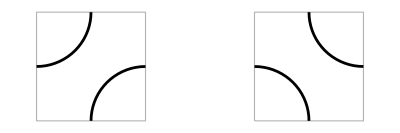

```mathematica
Graphics[{plaquette[0,{0,0}],plaquette[1,{2,0}]}]
```

Putting together many of these plaquettes produces a collection of loops and paths (reminiscent of Fully Packed Loops, but not quite the same):

```mathematica
myplaquettes=randombits[10,10];
Graphics[plaquettes[myplaquettes]]
```

(Connoisseurs of percolation theory will recognize that this is a disguised version of critical bond percolation on the square lattice.)

### The connectivity pattern of loop percolation

What we’ll do is to consider this as an arrangement of plaquettes on a cylinder, by identifying the left and right boundary edges of the big square. The paths then connect boundary points on the bottom and top edges (the “lids” of the cylinder) to each other in some complicated pattern.

```mathematica
plaquettegr=Graphics[{plaquettes[myplaquettes],Table[plaquettesendpointpathgraphics[myplaquettes,j,ColorData["Rainbow"][(j-1)/9]],{j,1,10}]},ImageSize->400];
Row[{plaquettegr, CylinderGraphics[plaquettegr]}]
```

We’re interested in the connectivity pattern that emerges between the bottom boundary endpoints. Imagine now the cylinder to be infinitely long, extending upwards all the way to infinity. The bottom boundary endpoints become more and more likely to be interconnected among themselves -- in other words to define a noncrossing matching.

```mathematica
CreatePalette[LoopPercolationInteractiveDemo[],WindowTitle->"Loop Percolation"];
```

Notice what happens in the randomized setting when the plaquette bias becomes very close to 0 or 1. In this case the model converges to a limiting process called pipe percolation.

## Pipe percolation

In pipe percolation (a.k.a. the Temperley-Lieb random walk, Temperley-Lieb stochastic process), we lay down a sequence of graphical pipe operators that act on noncrossing matchings.

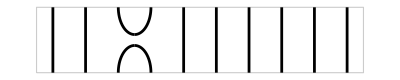

```mathematica
Graphics[{AbsoluteThickness[2],PipeOperatorGraphics[10,3,0]}]
```

In this representation, the jth operator has the effect of matching points j and j+1, and rerouting the point previously matched to j to the point that was matched to j+1. For each operator, j is chosen uniformly at random from the integers 1,...,2n.

```mathematica
CreatePalette[PipePercolationInteractiveDemo[],WindowTitle->"Pipe Percolation"];
```

## All loops lead to Rome

We defined random noncrossing matchings obtained as the connectivity patterns of several different processes: Fully Packed Loop arrangements, loop percolation, and pipe percolation. There are several amazing connections between these different random objects.

### The connectivity pattern of loop percolation is independent of the plaquette bias 0<p<1

This property observed by Di Francesco, Zinn-Justin (2006) and possibly others. Catch phrase: “Loop percolation is integrable”

Technically, the row-transfer matrices T_n^(p) all commute with each other, therefore share the same Frobenius-Perron eigenvector

Proof using a beautiful algebraic technique -- the Yang-Baxter equation

New proof (R.+Peled 2014) using an explicit combinatorial bijection

### The connectivity pattern of pipe percolation is the same as that of loop percolation

Follows easily from the above invariance result by taking the limit as p→0

### The Cantini-Sportiello-Razumov-Stroganov theorem

In 2001, Alexander Razumov and Yuri Stroganov, and independently Murray Batchelor, Jan de Gier and Bernard Nienhuis, numerically computed the distribution of the connectivity pattern of pipe percolation (equivalently: the stationary distribution of the Temperley-Lieb random walk). Let’s follow in their footsteps:

```mathematica
Manipulate[Column[{Apply[Plus, #], #}] &@RazumovStroganovEigenvector[n], {n, 1, 7, 1}]
```

Razumov and Stroganov recognized that the coordinates of the vector enumerated Fully Packed Loops, and formulated a conjecture, which was proved in 2010 by Luigi Cantini and Andrea Sportiello:

The Cantini-Sportiello-Razumov-Stroganov theorem. The probability in pipe percolation/loop percolation (of order n) for a given connectivity pattern α is equal to the number of FPL arrangements (of order n) whose connectivity pattern is equal to α divided by the total number FPL_n of arrangements.

Equivalently: the connectivity pattern of a uniformly random FPL arrangement is equal in distribution to that of loop percolation (with any bias p) and pipe percolation.

Cantini and Sportiello’s proof is ingenious and highly nontrivial. A variant of Wieland’s gyration map plays a key role.

## Rational probabilities of connectivity events

In numerical work around 2001-2004, D. Wilson, J.-B. Zuber and Mitra-Nienhuis-de Gier-Batchelor found simple formulas for probabilities of simple events in the Razumov-Stroganov distribution on noncrossing matchings (the distribution of the connectivity pattern of loop percolation, Fully Packed Loops etc.).

### Example: The submatching event “”

```mathematica
Table[ProbabilityForSubmatchingEvent[n,{2,1}],{n,1,6}]
```

```mathematica
GuessFormula[%,{n,1,6},1]
```

### Example: The submatching event “”

```mathematica
Table[ProbabilityForSubmatchingEvent[n,{2,1,4,3}],{n,2,6}]
```

```mathematica
GuessFormula[%,{n,2,6},2]
```

### Other examples

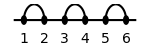
```mathematica
{{Event, Probability, Probability as n→∞}, {-Graphics-, 3/2×(n^2+1)/(4 n^2-1), 3/8}, {-Graphics-, 1/8×(97 n^6+82 n^4-107 n^2-792)/((4 n^2-1)^2(4 n^2-9)), 97/512}, {-Graphics-, 1/16×(59 n^6+299 n^4+866 n^2+576)/((4 n^2-1)^2(4 n^2-9)), 59/1024}, {-Graphics-, 1/512×(214093 n^12-980692 n^10-584436 n^8-1887916 n^6+1361443 n^4-17432892 n^2-316353600)/((4 n^2-1)^3(4 n^2-9)^2(4 n^2-25)), 214093/2^21}}
```

### Theoretical developments

The formula for the probability of the simplest submatching event “” was proved in 2009 (Fonseca-Zinn-Justin 2009).

Using the “qKZ equation” techniques developed by Di Francesco-Zinn Justin (2006) and Fonseca-Zinn-Justin, I proved a couple of the other conjectured formulas (R. 2014).

In the same paper, I also proved a general formula expressing the probability of an arbitrary submatching event as a constant term of a certain multivariate Laurent polynomial. It’s not clear yet how to see that this complicated algebraic expression is always a rational function of n (the obvious empirical pattern one observes in the simple cases). This is an interesting conjecture in algebraic combinatorics with beautiful probabilistic consequences (especially in the limit as n→∞).

My constant term formula was discovered experimentally using Mathematica. In fact, I wrote Mathematica code specifically looking for a certain kind of algebraic expansion (relating a sum over a certain class of “wheel polynomials” to another sum involving a different basis of the same vector space; see my paper). Thus, using a combination of intuition, patience and coding skills I was able to discover (and eventually prove) a beautiful mathematical theorem.

(Moral of the story: good programming skills can make you look smarter than you are!)

## Razumov-Stroganov conjectures and symmetry classes of FPLS

Razumov and Stroganov also studied several natural variants of pipe percolation and the associated Temperley-Lieb random walk with different boundary conditions, and discovered numerically a host of similar “Razumov-Stroganov conjectures” relating the associated eigenvector with classes of FPL arrangements. A few of them were also proved by Cantini and Sportiello using their generalized gyration; others are still unsolved.

### Example: aperiodic boundary conditions and Vertically Symmetric FPLs

Thinking of noncrossing matchings as objects existing on a line rather than a circle, it is natural to disallow the “wraparound” pipe operator connecting the points 1 and 2n. The associated stationary distribution no longer has rotational symmetry. Let’s explore this.

```mathematica
eigenvectors=Table[RazumovStroganovAperiodicEigenvector[n], {n, 1, 7, 1}];
Manipulate[Column[{Apply[Plus, #], #}] &@eigenvectors[[n]], {n, 1, 7, 1}]
```

```mathematica
Map[Apply[Plus,#]&,eigenvectors]
```

```mathematica
OnlineEncyclopediaOfIntegerSequencesLookup[%]
```

It turns out that the stationary probabilities are related to the connectivity patterns of uniformly random FPL arrangements chosen from the set of Vertically Symmetric FPLs (related to Vertically Symmetric Alternating Sign Matrices, known as VSASMs).

### Other Razumov-Stroganov variants

The Razumov-Stroganov conjectures involve symmetry classes of FPLs, or equivalently of ASMs. Here our story intersects with another story -- the enumeration of these symmetry classes (mostly solved in two papers by Greg Kuperberg and Soichi Okada). Some of the symmetry classes that show up are:

Half-Turn Symmetric ASMs (HTASM)

Quarter-Turn Symmetric ASMs (QTASM)

Diagonally and Antidiagonally Symmetric ASMs (DASASM)

... (?)

## The End - Thank You!

```mathematica
Style[FunFPLAnimation[10],TextAlignment->Center]
```

### References

Ben Wieland. A large dihedral symmetry of the set of alternatign sign matrices. Elect. J. Combin. 7 (2000), #R37.

Alexander Razumov, Yuri Stroganov. Combinatorial nature of ground state vector of O(1) loop model. Theor. Math. Phys. 138 (2004), 333-337.

Luigi Cantini, Andrea Sportiello. Proof of the Razumov-Stroganov conjecture. J. Comb. Theory Ser. A 118 (2011), 1549-1574.

Dan Romik. Connectivity patterns in loop percolation I: the rationality phenomenon and constant term identities. Commun. Math. Phys. 330 (2014), 499-538.

Dan Romik, Ron Peled. Bijective combinatorial proof of the commutation of transfer matrices in the dense O(1) loop model. Preprint, 2014.